```mathematica
soURL="http://localhost:12612"
```

http://localhost:12612

```mathematica
soIndexURL=soURL<>"/so-index/"
```

http://localhost:12612/so-index/

```mathematica
soMediaURL=soURL<>"/so-media/"
```

http://localhost:12612/so-media/

```mathematica
secucode="600318"
```

600318

```mathematica
secuname="新力金融"
```

新力金融

```mathematica
Import[soIndexURL<>secucode,"RawJSON"];
```

```mathematica
codeIndex=Import[soIndexURL<>secucode,"RawJSON"];
```

```mathematica
nameIndex=Import[soIndexURL<>secuname,"RawJSON"];
```

```mathematica
codeMedia=Import[soMediaURL<>secucode,"RawJSON"];
```

```mathematica
nameMedia=Import[soMediaURL<>secuname,"RawJSON"];
```

```mathematica
codeIndexData = codeIndex[["data"]]//StringSplit[#,"|"]&;
```

```mathematica
codeIndexFrom=DateObject[codeIndex[["from"]]];
```

```mathematica
yyyymmdd[date_]:=DateString[date,{"Year","Month","Day"}]
```

```mathematica
codeIndexDateList=NestList[DatePlus[#,1]&,codeIndexFrom,(codeIndexData//Length)-1];
```

```mathematica
codeIndexAssoc=AssociationThread[yyyymmdd/@codeIndexDateList,ToExpression/@codeIndexData];
```

```mathematica
dateRange={50,1000};
```

```mathematica
codeIndexAssocPart = codeIndexAssoc//Take[#,dateRange]&;
```

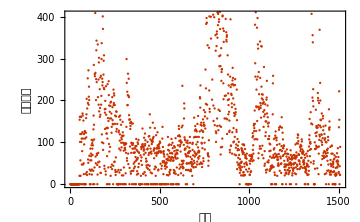

```mathematica
ListPlot[#,PlotTheme->"Web",ImageSize->Medium,AxesLabel->{"日期","搜索指数"},Ticks->{Keys@#,Values@#},PlotLegends->None,LabelingFunction->None]&@codeIndexAssoc
```

```mathematica
ListPlot[#,PlotTheme->"Web",ImageSize->Medium,AxesLabel->{"日期","搜索指数"},Ticks->{Keys@#,Values@#},PlotLegends->None,LabelingFunction->None]&@nameIndexAssoc
```

```mathematica
kURL="https://www.joudou.com/stockinfogate/kchartdata/"<>secucode;
```

```mathematica
kData=Import[kURL,"RawJSON"][["data"]];
```

```mathematica
turnoverData=Select[kData[["turnover"]],#[[1]]>20130110&];
```

```mathematica
ratioData=#[[4]]&/@turnoverData;
```

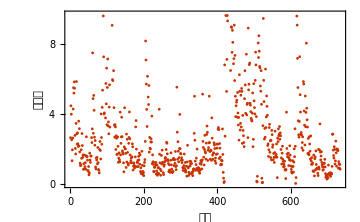

```mathematica
ListPlot[#,PlotTheme->"Web",ImageSize->Medium,AxesLabel->{"日期","换手率"},PlotLegends->None]&@ratioData
```

```mathematica
forwardData=Select[kData[["restoration_forward"]],#[[1]]>20130110&];
```

```mathematica
fclosepriceData=#[[2]]&/@forwardData;
```

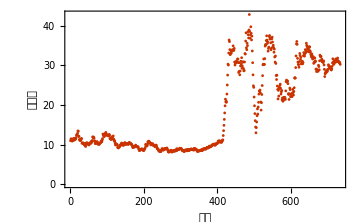

```mathematica
ListPlot[#,PlotTheme->"Web",ImageSize->Medium,AxesLabel->{"日期","收盘价"},PlotLegends->None]&@fclosepriceData
```